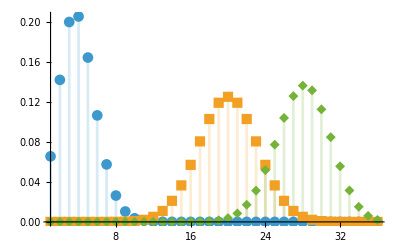

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,36},PlotRange->All,PlotMarkers->Automatic]
```

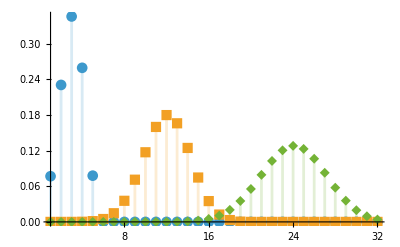

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[n,.6],k],{n,{5,20,40}}]//Evaluate,{k,32},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
PDF[BinomialDistribution[n,p],k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

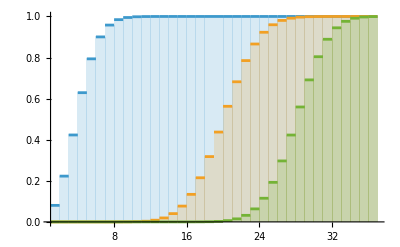

```mathematica
DiscretePlot[Table[CDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,36},ExtentSize->Right]
```

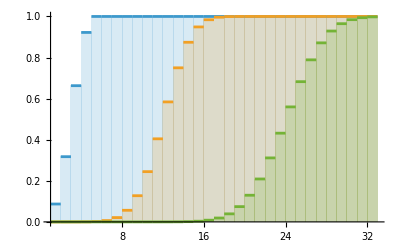

```mathematica
DiscretePlot[Table[CDF[BinomialDistribution[n,.6],k],{n,{5,20,40}}]//Evaluate,{k,32},ExtentSize->Right]
```

```mathematica
CDF[BinomialDistribution[n,p],k]
```

Piecewise[{{BetaRegularized[1-p,n-Floor[k],1+Floor[k]], 0≤k<n}, {1, k≥n}, {0, True}}]

```mathematica
Mean[BinomialDistribution[n,p]]
```

n p

```mathematica
Variance[BinomialDistribution[n,p]]
```

n (1-p) p

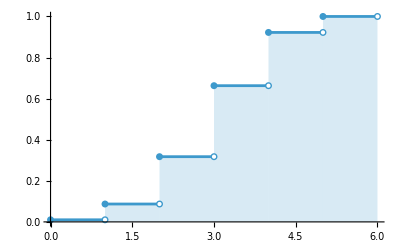

```mathematica
DiscretePlot[CDF[BinomialDistribution[5,.6],x],{x,0,5},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
CDF[BinomialDistribution[5,.6],x]//PiecewiseExpand
```

Piecewise[{{0.01024, 0≤x<1}, {0.08704, 1≤x<2}, {0.31744, 2≤x<3}, {0.66304, 3≤x<4}, {0.92224, 4≤x<5}, {1, x≥5}, {0, True}}]

```mathematica
RandomVariate[BernoulliDistribution[0.75],10]/.{0->"Miss",1->"Hit"}
```

{Hit,Hit,Hit,Hit,Hit,Hit,Hit,Hit,Hit,Hit}

```mathematica
Probability[x==2,x\[Distributed]BinomialDistribution[3,0.75]]
```

0.421875

```mathematica
Probability[x==0,x\[Distributed]BinomialDistribution[3,0.75]]Probability[x==2,x\[Distributed]BinomialDistribution[2,0.75]]
```

0.00878906

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[n,0.75]]
```

0.75 n

```mathematica
RandomVariate[BernoulliDistribution[0.300],5]
```

{1,0,0,0,0}

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[3,0.300]]
```

0.9

```mathematica
Probability[x≥3,x\[Distributed]BinomialDistribution[4,0.3]]
```

0.0837

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[500,0.3]]
```

150.

```mathematica
heads[n_]:=BinomialDistribution[n,1/2]
```

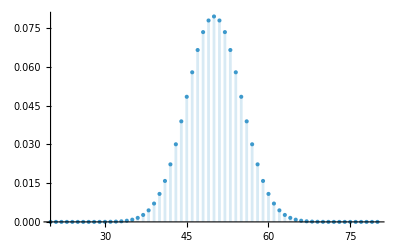

```mathematica
DiscretePlot[PDF[heads[100],k],{k,20,80},PlotRange->All]
```

```mathematica
Probability[60≤x≤80,x\[Distributed]heads[100]]
```

18028505720779282715431630437/633825300114114700748351602688

```mathematica
uheads[n_]:=BinomialDistribution[n,0.6];
```

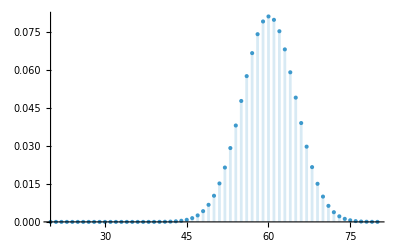

```mathematica
DiscretePlot[PDF[uheads[100],k],{k,20,80},PlotRange->All]
```

```mathematica
Probability[60≤x≤80,x\[Distributed]uheads[100]]
```

0.543289

```mathematica
defective[n_]:=BinomialDistribution[n,1/10]
```

```mathematica
Probability[x≤1,x\[Distributed]defective[5]]
```

45927/50000

```mathematica
N[]
```

0.91854

```mathematica
prob1=Probability[x≤2,x\[Distributed]BinomialDistribution[4,p]]
```

(-1+p)^2 (1+2 p+3 p^2)

```mathematica
prob2=Probability[x≤1,x\[Distributed]BinomialDistribution[2,p]]
```

1-p^2

```mathematica
Reduce[prob1>prob2&&0<p<1,p]
```

0<p<1/3

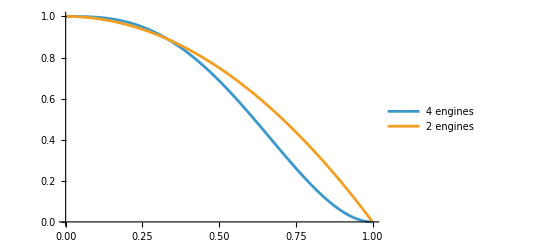

```mathematica
Plot[{prob1,prob2},{p,0,1},PlotLegends->{"4 engines","2 engines"}]
```

```mathematica
Probability[x≥1,x\[Distributed]BinomialDistribution[3,Exp[-λ t]]]
```

1-(1-ⅇ^(-t λ))^3

```mathematica
Reduce[(%/.λ->10^-8)≤0.99,t,Reals]//Quiet
```

t≥2.42637×10^7

```mathematica
Last[] / (3600 * 24 * 365)
```

0.769396

```mathematica
Table[Probability[x==k,x\[Distributed]BinomialDistribution[100,0.01]],{k,{0,2,5,10}}]
```

{0.366032,0.184865,0.00289779,7.00604×10^-8}

```mathematica
Probability[x≥1,x\[Distributed]BinomialDistribution[n,10^-4]]//Simplify[#,n>0]&
```

1-(9999/10000)^n

```mathematica
Reduce[0≤%≤10^-3,n,Integers]
```

n∈ℤ&&0≤n≤10

```mathematica
Probability[x≥1,x\[Distributed]PoissonDistribution[n 10^-4]]
```

1-ⅇ^(-n/10000)

```mathematica
Reduce[0≤%≤10^-3,n,Integers]
```

n∈ℤ&&0≤n≤10

```mathematica
PDF[BinomialDistribution[n,p],k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

```mathematica
Probability[x>c,x\[Distributed]BinomialDistribution[n,p],Assumptions->c∈Integers&&0≤c≤n]
```

Piecewise[{{(Beta[p,1+c,-c+n] Gamma[1+n])/(Gamma[1+c] Gamma[-c+n]), 1+c≤n}, {0, True}}]

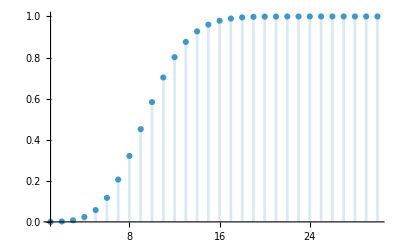

```mathematica
DiscretePlot[CDF[BinomialDistribution[100,0.1],c],{c,30}]
```

```mathematica
Minimize[{c,CDF[BinomialDistribution[100,1/10],c]≥999/1000&&0<c≤100},c,Integers]
```

{20,{c→20}}

```mathematica
{CDF[BinomialDistribution[100,0.1],19],CDF[BinomialDistribution[100,0.1],20]}
```

{0.998021,0.999192}

```mathematica
p=With[{𝒟=DiscreteUniformDistribution[{1,6}]},Probability[k1+k2>=10,k1\[Distributed]𝒟&&k2\[Distributed]𝒟]]
```

1/6

```mathematica
{pay1,pay2}={9,4};
{pay1 p, pay2(1-p)}//N
```

{1.5,3.33333}

```mathematica
f=FunctionExpand[Probability[pay1*k>pay2*(n-k),k\[Distributed]BinomialDistribution[n,p]],n∈Integers&&n≥1]
```

Piecewise[{{6^-n (-5^n+6^n), 1<n<13/4}, {5^(-1+n) 6^-n n, n==1}, {(5^(-1+n-Floor[(4 n)/13]) 6^-n Gamma[1+n] Hypergeometric2F1[1,1-n+Floor[(4 n)/13],2+Floor[(4 n)/13],-1/5])/(Gamma[n-Floor[(4 n)/13]] Gamma[2+Floor[(4 n)/13]]), n≥13/4}, {0, True}}]

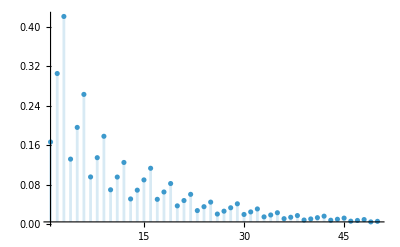

```mathematica
DiscretePlot[f,{n,50},PlotRange->All]
```

```mathematica
Maximize[{f,1<n<50},n,Integers]
```

{91/216,{n→3}}